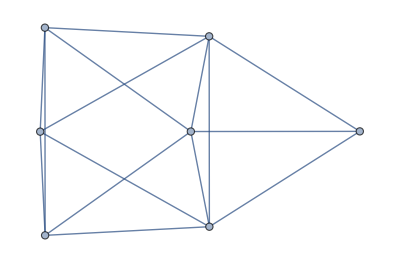
BeautiGraph[-Graphics-]

```mathematica
BeautiGraph [ReadGrof[6]]
```

```mathematica
FindB4CReduction[ReadGrof[6]]
```

FindB4CReduction[-Graphics-]

```mathematica
MakeComplete[v_]:=Map[#[[1]]<->#[[2]]&,Subsets[v,{2}]]
```

```mathematica
MakeComplete[Range[3]]
```

{1<->2,1<->3,2<->3}

```mathematica
BeautiGraph[g_]:=Graph[MakeComplete[Sort[VertexList[g]]],GraphHighlight->EdgeList[GraphComplement[g]], GraphHighlightStyle->"Thick", VertexLabels->"Name", EdgeStyle->LightGray]
```

```mathematica
FindB4CReduction[g_]:=Block[{
Candidates=BarelyFourColorableGraphsOfCount[VertexCount[g]], 
edgeCount=EdgeCount[g], 
difference,
new,
iso,
can2,
result
},
Select[
Flatten[
Table[
difference=EdgeCount[can]-EdgeCount[g];
If[difference==0 ,
If[IsomorphicGraphQ[can,g],
{}<->BeautiGraph[can], Null]
,
Table[
new=EdgeAdd[g,s];
If[IsomorphicGraphQ[new,can],
iso=First[FindGraphIsomorphism [can,new]];
can2=Map[(#[[1]]/.Normal[iso])<->(#[[2]]/.Normal[iso])&,EdgeList[can]];
result=Graph[BeautiGraph[Graph[VertexList[g],can2]],EdgeStyle->Map[#->{Darker[Green],Thick}&,s],ImageSize->120];
result
,
Null
]
,{s,Subsets[EdgeList[GraphComplement[g]],{difference}]}
]
]
,{can,Candidates}
]

],
#=!=Null&
]
]
```

```mathematica
SameEdge[e1_,e2_]:=(e1[[1]]==e2[[1]]&&e1[[2]]==e2[[2]])||(e1[[1]]==e2[[2]]&&e1[[2]]==e2[[1]])
```

```mathematica
SortEdge[e_]:=If[e[[1]]<e[[2]],e,UndirectedEdge[e[[2]],e[[1]]]]
```

```mathematica
NormalizeEdges[l_]:=Sort[Map[SortEdge,l]]
```

```mathematica
GetOption[object_,name_]:=First[AbsoluteOptions[object,name]][[2]]
```

```mathematica
ContractReduction[g_,e_]:=Block[{sol=FindB4CReduction[VertexContract[g,{e[[1]],e[[2]]}]],away,env,color,comp=CompleteGraph[VertexCount[g],GraphLayout->"CircularEmbedding"],pos, highlight, edges,e2},
e2=SortEdge[e];
away=e[[2]];
sol=Map[VertexAdd[#,away]&,sol];
env=Map[SortEdge,EdgeList[g,away<->_]];
color=First[Options[sol[[1]],EdgeStyle]][[2]];
highlight=First[Options[sol[[1]],GraphHighlight]][[2]];
pos=First[AbsoluteOptions[comp,VertexCoordinates]][[2]];
edges=Map[SortEdge,Table[away<->k,{k,Select[VertexList[g],#≠away&]}]];
color=Join[color,Map[If[SameEdge[e2,#] ,#->{Thickness[0.03],Yellow},#->{Thick,Blue}]&,Select[edges,SameEdge[e2,#]||!MemberQ[env,#]&]]];
sol=Map[With[{
g2=EdgeAdd[#,edges]},
Graph[
Sort[VertexList[g2]],
EdgeList[g2],
EdgeStyle->color,
VertexCoordinates->pos,
GraphHighlight->highlight,
GraphHighlightStyle->"Thick",
VertexLabels->"Name",ImageSize->120]
]&,sol];
sol
]
```

```mathematica
EdgeList[ReadGrof[6]]
```

{1<->2,1<->3,1<->5,1<->7,2<->3,2<->6,2<->7,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6,5<->7,6<->7}

```mathematica
FindB4CReduction[ReadGrof[6]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{g=ReadGrof[6]},
{Map[Framed,FindB4CReduction[g]],Table[e<->{FindB4CReduction[EdgeDelete[g,e]],ContractReduction[g,e]},{e,CollectMPGEdges[g]}]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1<->2<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},1<->3<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},1<->5<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},1<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},2<->3<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},2<->6<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},2<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},3<->4<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},4<->5<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},4<->6<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},5<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},6<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}}}}

```mathematica
With[{g=ReadGrof[7]},
{Map[Framed,FindB4CReduction[g]],Table[e<->{FindB4CReduction[EdgeDelete[g,e]],ContractReduction[g,e]},{e,CollectMPGEdges[g]}]}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{1<->2<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},1<->3<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},1<->5<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},1<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},2<->3<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},2<->5<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},2<->6<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},3<->4<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},3<->6<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},3<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},4<->5<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},4<->6<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},4<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}},5<->6<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}},5<->7<->{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-}}}}